```mathematica
Дистиллированная вода. Эффект батареи: при отключении источника тока в любой точке вольтметр показывает 0.1 В.  Общее: 2В, 0 мА, 135 кОм между электродами;
Flatten[Table[{i, j, 1}, {i, -15, 15}, {j, -10, 10}], 1]
```

```mathematica
data = {{-15,-10,1.32},{-15,-9,1.34},{-15,-8,1.35},{-15,-7,1.37},{-15,-6, 1.39},{-15,-5,1.4},{-15,-4,1.43},{-15,-3,1.44},{-15,-2,1.45},{-15,-1,1.45},{-15,0,1.3},{-15,1,1.44},{-15,2,1.43},{-15,3,1.41},{-15,4,1.39},{-15,5,1.37},{-15,6,1.36},{-15,7,1.35},{-15,8,1.33},{-15,9,1.32},{-15,10,1.31},{-14,-10,1.34},{-14,-9,1.34},{-14,-8,1.35},{-14,-7,1.36},{-14,-6,1.37},{-14,-5,1.38},{-14,-4,1.4},{-14,-3,1.41},{-14,-2,1.42},{-14,-1,1.43},{-14,0,1.43},{-14,1,1.43},{-14,2,1.42},{-14,3,1.4},{-14,4,1.38},{-14,5,1.36},{-14,6,1.35},{-14,7,1.33},{-14,8,1.31},{-14,9,1.3},{-14,10,1.28},{-13,-10,1.32},{-13,-9,1.33},{-13,-8,1.34},{-13,-7,1.35},{-13,-6,1.36},{-13,-5,1.38},{-13,-3,1.42},{-13,-2,1.45},{-13,-1,1.46},{-13,0,1.47},{-13,1,1.45},{-13,2,1.42},{-13,3,1.4},{-13,4,1.38},{-13,5,1.35},{-13,6,1.33},{-13,7,1.31},{-13,8,1.31},{-13,9,1.29},{-13,10,1.28},{-12,-10,1.32},{-12,-9,1.33},{-12,-8,1.34},{-12,-7,1.35},{-12,-6,1.37},{-12,-5,1.39},{-12,-4,1.41},{-12,-3,1.44},{-12,-2,1.46},{-12,-1,1.5},{-12,0,1.51},{-12,1,1.49},{-12,2,1.46},{-12,3,1.4},{-12,4,1.37},{-12,5,1.34},{-12,6,1.31},{-12,7,1.29},{-12,8,1.27},{-12,9,1.25},{-12,10,1.24},{-11,-10,1.26},{-11,-9,1.28},{-11,-8,1.29},{-11,-7,1.3},{-11,-6,1.32},{-11,-5,1.34},{-11,-4,1.37},{-11,-3,1.4},{-11,-2,1.44},{-11,-1,1.5},{-11,0,1.55},{-11,1,1.49},{-11,2,1.42},{-11,3,1.37},{-11,4,1.33},{-11,5,1.3},{-11,6,1.28},{-11,7,1.26},{-11,8,1.24},{-11,9,1.22},{-11,10,1.21},{-10,-10,1.24},{-10,-9,1.26},{-10,-8,1.27},{-10,-7,1.29},{-10,-6,1.3},{-10,-5,1.32},{-10,-4,1.35},{-10,-3,1.38},{-10,-2,1.43},{-10,-1,1.52},{-10,1,1.47},{-10,2,1.4},{-10,3,1.35},{-10,4,1.31},{-10,5,1.28},{-10,6,1.25},{-10,7,1.23},{-10,8,1.22},{-10,9,1.22},{-10,10,1.18},{-9,-10,1.21},{-9,-9,1.22},{-9,-8,1.22},{-9,-7,1.23},{-9,-6,1.25},{-9,-5,1.27},{-9,-4,1.29},{-9,-3,1.33},{-9,-2,1.37},{-9,-1,1.42},{-9,0,1.46},{-9,1,1.42},{-9,2,1.36},{-9,3,1.32},{-9,4,1.28},{-9,5,1.25},{-9,6,1.22},{-9,7,1.19},{-9,8,1.18},{-9,9,1.16},{-9,10,1.16},{-8,-10,1.17},{-8,-9,1.18},{-8,-8,1.19},{-8,-7,1.21},{-8,-6,1.22},{-8,-5,1.24},{-8,-4,1.26},{-8,-3,1.29},{-8,-2,1.32},{-8,-1,1.34},{-8,0,1.36},{-8,1,1.34},{-8,2,1.31},{-8,3,1.26},{-8,4,1.24},{-8,5,1.21},{-8,6,1.19},{-8,7,1.18},{-8,8,1.16},{-8,9,1.14},{-8,10,1.13},{-7,-10,1.17},{-7,-9,1.18},{-7,-8,1.19},{-7,-7,1.2},{-7,-6,1.22},{-7,-5,1.24},{-7,-4,1.26},{-7,-3,1.29},{-7,-2,1.31},{-7,-1,1.33},{-7,0,1.35},{-7,1,1.34},{-7,2,1.31},{-7,3,1.27},{-7,4,1.23},{-7,5,1.21},{-7,6,1.19},{-7,7,1.17},{-7,8,1.16},{-7,9,1.14},{-7,10,1.13},{-6,-10,1.15},{-6,-9,1.16},{-6,-8,1.17},{-6,-7,1.18},{-6,-6,1.19},{-6,-5,1.21},{-6,-4,1.23},{-6,-3,1.24},{-6,-2,1.26},{-6,-1,1.27},{-6,0,1.28},{-6,1,1.27},{-6,2,1.25},{-6,3,1.22},{-6,4,1.2},{-6,5,1.18},{-6,6,1.16},{-6,7,1.15},{-6,8,1.13},{-6,9,1.12},{-6,10,1.1},{-5,-10,1.1},{-5,-9,1.11},{-5,-8,1.12},{-5,-7,1.13},{-5,-6,1.13},{-5,-5,1.14},{-5,-4,1.15},{-5,-3,1.16},{-5,-2,1.16},{-5,-1,1.15},{-5,0,1.13},{-5,1,1.12},{-5,2,1.11},{-5,3,1.1},{-5,4,1.11},{-5,5,1.1},{-5,6,1.09},{-5,7,1.09},{-5,8,1.08},{-5,9,1.07},{-5,10,1.06},{-4,-10,1.06},{-4,-9,1.09},{-4,-8,1.1},{-4,-7,1.1},{-4,-6,1.11},{-4,-5,1.11},{-4,-4,1.11},{-4,-3,1.12},{-4,-2,1.13},{-4,-1,1.12},{-4,0,1.105},{-4,1,1.09},{-4,2,1.09},{-4,3,1.08},{-4,4,1.07},{-4,5,1.07},{-4,6,1.06},{-4,7,1.06},{-4,8,1.05},{-4,9,1.04},{-4,10,1.04},{-3,-10,1.03},{-3,-9,1.04},{-3,-8,1.05},{-3,-7,1.07},{-3,-6,1.08},{-3,-5,1.08},{-3,-4,1.09},{-3,-3,1.09},{-3,-2,1.09},{-3,-1,1.08},{-3,0,1.07},{-3,1,1.07},{-3,2,1.06},{-3,3,1.05},{-3,4,1.04},{-3,5,1.04},{-3,6,1.03},{-3,7,1.03},{-3,8,1.02},{-3,9,1.02},{-3,10,1.01},{-2,-10,1.0},{-2,-9,1.0},{-2,-8,1.01},{-2,-7,1.03},{-2,-6,1.04},{-2,-5,1.04},{-2,-4,1.04},{-2,-3,1.04},{-2,-2,1.04},{-2,-1,1.03},{-2,0,1.025},{-2,1,1.02},{-2,2,1.02},{-2,3,1.02},{-2,4,1.02},{-2,5,1.01},{-2,6,1.01},{-2,7,1.02},{-2,8,1.02},{-2,9,1.01},{-2,10,1.0},{-1,-10,0.97},{-1,-9,0.98},{-1,-8,0.98},{-1,-7,0.98},{-1,-6,1.0},{-1,-5,1.0},{-1,-4,1.01},{-1,-3,1.0},{-1,-2,1.0},{-1,-1,1.0},{-1,0,0.99},{-1,1,0.99},{-1,2,.99},{-1,3,.98},{-1,4,.98},{-1,5,.98},{-1,6,0.98},{-1,7,0.98},{-1,8,0.98},{-1,9,0.98},{-1,10,0.97},{0,-10,0.99},{0,-9,0.99},{0,-8,1.0},{0,-7,1.0},{0,-6,1.0},{0,-5,1.0},{0,-4,1.0},{0,-3,1.0},{0,-2,1.0},{0,-1,0.99},{0,0,0.98},{0,1,.98},{0,2,.97},{0,3,.97},{0,4,.96},{0,5,.95},{0,6,.96},{0,7,.96},{0,8,.96},{0,9,.96},{0,10,.96},{1,-10,0.93},{1,-9,.93},{1,-8,.94},{1,-7,.94},{1,-6,.94},{1,-5,.94},{1,-4,.94},{1,-3,.94},{1,-2,.94},{1,-1,.94},{1,0,.93},{1,1,.93},{1,2,.93},{1,3,.93},{1,4,.95},{1,5,.95},{1,6,.95},{1,7,.95},{1,8,.945},{1,9,.945},{1,10,.945},{2,-10,.91},{2,-9,.91},{2,-8,.91},{2,-7,.91},{2,-6,.9},{2,-5,.9},{2,-4,.9},{2,-3,.9},{2,-2,.9},{2,-1,.895},{2,0,.895},{2,1,.895},{2,2,.895},{2,3,.895},{2,4,.9},{2,5,.9},{2,6,.905},{2,7,.905},{2,8,.91},{2,9,.91},{2,10,.91},{3,-10,.88},{3,-9,.875},{3,-8,.875},{3,-7,.87},{3,-6,.87},{3,-5,.86},{3,-4,.855},{3,-3,.85},{3,-2,.855},{3,-1,.85},{3,0,.85},{3,1,.855},{3,2,.855},{3,3,.86},{3,4,.86},{3,5,.87},{3,6,.87},{3,7,.88},{3,8,.88},{3,9,.885},{3,10,.89},{4,-10,.85},{4,-9,.85},{4,-8,.845},{4,-7,.845},{4,-6,.84},{4,-5,.83},{4,-4,.82},{4,-3,.82},{4,-2,.81},{4,-1,.81},{4,0,.813},{4,1,.814},{4,2,.816},{4,3,.823},{4,4,.83},{4,5,.84},{4,6,.85},{4,7,.85},{4,8,.86},{4,9,.865},{4,10,.87},{5,-10,.815},{5,-9,.81},{5,-8,.81},{5,-7,.8},{5,-6,.793},{5,-5,.78},{5,-4,.78},{5,-3,.77},{5,-2,.76},{5,-1,.76},{5,0,.76},{5,1,.767},{5,2,.77},{5,3,.78},{5,4,.79},{5,5,.8},{5,6,.81},{5,7,.82},{5,8,.83},{5,9,.83},{5,10,.84},{6,-10,.79},{6,-9,.787},{6,-8,.78},{6,-7,.775},{6,-6,.765},{6,-5,.75},{6,-4,.74},{6,-3,.73},{6,-2,.72},{6,-1,.71},{6,0,.705},{6,1,.71},{6,2,.714},{6,3,.73},{6,4,.74},{6,5,.755},{6,6,.77},{6,7,.777},{6,8,.79},{6,9,.805},{6,10,.81},{7,-10,.76},{7,-9,.76},{7,-8,.75},{7,-7,.74},{7,-6,.73},{7,-5,.72},{7,-4,.71},{7,-3,.69},{7,-2,.675},{7,-1,.66},{7,0,.647},{7,1,.655},{7,2,.666},{7,3,.69},{7,4,.7},{7,5,.72},{7,6,.74},{7,7,.75},{7,8,.77},{7,9,.777},{7,10,.78},{8,-10,.74},{8,-9,.735},{8,-8,.73},{8,-7,.715},{8,-6,.7},{8,-5,.685},{8,-4,.663},{8,-3,.64},{8,-2,.615},{8,-1,.595},{8,0,.58},{8,1,.59},{8,2,.61},{8,3,.64},{8,4,.66},{8,5,.685},{8,6,.7},{8,7,.72},{8,8,.73},{8,9,.745},{8,10,.75},{9,-10,.7},{9,-9,.695},{9,-8,.693},{9,-7,.69},{9,-6,.68},{9,-5,.67},{9,-4,.653},{9,-3,.633},{9,-2,.603},{9,-1,.57},{9,0,.483},{9,1,.52},{9,2,.555},{9,3,.6},{9,4,.628},{9,5,.655},{9,6,.676},{9,7,.692},{9,8,.705},{9,9,.72},{9,10,.73},{10,-10,.68},{10,-9,.678},{10,-8,.67},{10,-7,.66},{10,-6,.645},{10,-5,.63},{10,-4,.608},{10,-3,.584},{10,-2,.54},{10,-1,.477},{10,1,.45},{10,2,.52},{10,3,.57},{10,4,.604},{10,5,.63},{10,6,.66},{10,7,.676},{10,8,.688},{10,9,.7},{10,10,.71},{11,-10,.666},{11,-9,.666},{11,-8,.658},{11,-7,.65},{11,-6,.636},{11,-5,.62},{11,-4,.6},{11,-3,.572},{11,-2,.535},{11,-1,.487},{11,0,.455},{11,1,.48},{11,2,.53},{11,3,.565},{11,4,.6},{11,5,.622},{11,6,.643},{11,7,.662},{11,8,.675},{11,9,.689},{11,10,.7},{12,-10,.65},{12,-9,.65},{12,-8,.644},{12,-7,.637},{12,-6,.626},{12,-5,0.61},{12,-4,.595},{12,-3,.573},{12,-2,.546},{12,-1,.525},{12,0,.505},{12,1,.52},{12,2,.542},{12,3,.57},{12,4,.596},{12,5,.618},{12,6,.635},{12,7,.65},{12,8,.667},{12,9,.68},{12,10,.69},{13,-10,.63},{13,-9,.627},{13,-8,.623},{13,-7,.617},{13,-6,.611},{13,-5,0.603},{13,-4,0.587},{13,-3,.573},{13,-2,.558},{13,-1,.545},{13,0,.543},{13,1,.547},{13,2,.558},{13,3,.575},{13,4,.585},{13,5,.612},{13,6,.627},{13,7,.642},{13,8,.657},{13,9,.67},{13,10,.68},{14,-10,.623},{14,-9,.62},{14,-8,.615},{14,-7,.61},{14,-6,.604},{14,-5,.596},{14,-4,.582},{14,-3,.59},{14,-2,.587},{14,-1,.573},{14,0,.578},{14,1,.58},{14,2,.594},{14,3,.6},{14,4,.612},{14,5,.625},{14,6,.636},{14,7,.65},{14,8,.66},{14,9,.665},{14,10,.67}};
```

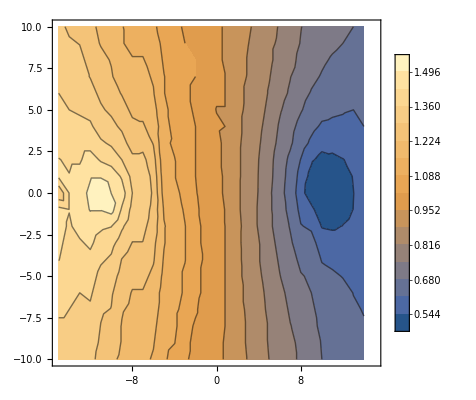

```mathematica
exp2 = ListContourPlot[data, PlotLegends -> Automatic, Contours->15, PlotRange-> {{-15, 15},{-10, 10}}]
```

```mathematica
ListPointPlot3D[data, ColorFunction -> "Rainbow"]
Length[data]
```

-Graphics3D-

```mathematica
Table[{data[[i, 1]], data[[i, 2]]}, {i, Length[data]}];
color = Table[-data[[i, 3]]*0.78/2+0.78, {i, Length[data]}];
```

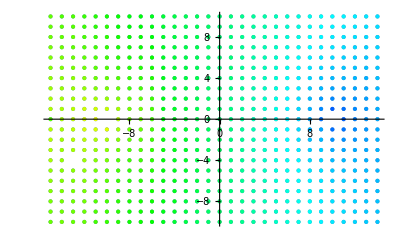

```mathematica
ListPlot[Table[{data[[i, 1]], data[[i, 2]]}, {i, Length[data]}]] ;


exp2 = ListPlot[Table[Style[{data[[i, 1]], data[[i, 2]]}, Hue[color[[i]]]], {i, Length[data]}]]
```